```mathematica
massfn[mmax_,m0_,a_,t_]:=((1-(1-(m0/mmax)^(1/4))*E^(-a*t/(4*mmax^(1/4)))))^4*mmax
```

```mathematica
massdecay[mmax_,a_,t_]:=mmax*E^(-a*((-1*t)+8000))
```

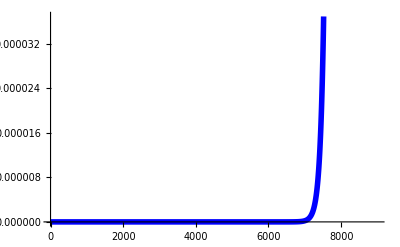

```mathematica
Plot[massdecay[100,.01,x],{x,0,9000},PlotStyle->{Thickness[.01],Blue}]
```

```mathematica
mmin=30
```

30

```mathematica
B0=4.7*10^(-2)
Em=5774(*J/gram*)
Emprime=7000
```

0.047

5774

7000

```mathematica
ain= B0/Em
aprime=B0/Emprime
```

8.13994×10^-6

6.71429×10^-6

```mathematica
massfn[mmax_,m0_,a_,t_]:=((1-(1-(m0/mmax)^(1/4))*E^(-a*t/(4*mmax^(1/4)))))^4*mmax
```

```mathematica
m0in=10^(-5);
```

```mathematica
?NMinimize
```

RowBox[{"NMinimize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] minimizes StyleBox["f", "TI"] numerically with respect to StyleBox["x", "TI"].
RowBox[{"NMinimize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] minimizes StyleBox["f", "TI"] numerically with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], StyleBox["…", "TR"]. 
RowBox[{"NMinimize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] minimizes StyleBox["f", "TI"] numerically subject to the constraints StyleBox["cons", "TI"].

```mathematica
tstart=x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-95],x>5000000},x][[2]]
```

6.75187×10^6

```mathematica
massfn[100,m0in,ain,tstart]
```

95.

```mathematica
massdecay[mmax_,a_,t_]:=.95*mmax*E^(-a/mmax^(1/4)*(t-tstart))
```

```mathematica
massdecay[100,ain,tstart]
```

95.

```mathematica
tfinish=x/.NMinimize[{Abs[massdecay[100,ain,x]-50],x>5000000},x][[2]]
```

7.00122×10^6

```mathematica
massdecay[100,ain,tfinish]
```

50.

```mathematica
mintime=x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-massdecay[100,ain,3000000]],x>5000000},x][[2]]
```

5.50001×10^7

```mathematica
massdecay[100,ain,8000000]
```

3.8232

```mathematica
recoverstart=massdecay[100,ain,.95*tstart]
```

226.528

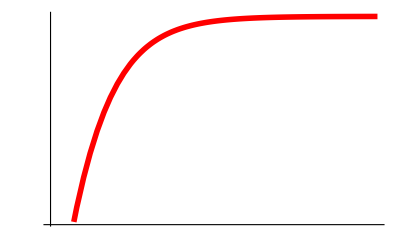

```mathematica
Plot[massfn[100,50,ain,x],{x,10,2*tfinish},PlotStyle->{Thickness[.01],Red},Ticks->False]
```

```mathematica
x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-50],x>5000000},x][[2]]
```

5.×10^6

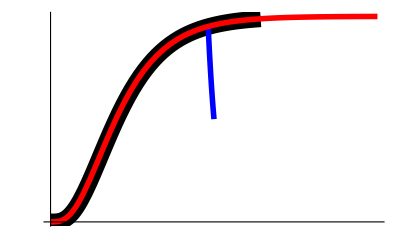

```mathematica
Show[
{
Plot[massfn[100,m0in,ain,x],{x,0,9000000},PlotStyle->{Thickness[.03],Black},Ticks->False,AxesStyle->Thickness[.005]],
Plot[massdecay[100,ain,x],{x,tstart,tfinish},PlotStyle->{Thickness[.01],Blue}],
Plot[massfn[100,50,ain,x-2.8*10^6],{x,0,2*tfinish},PlotStyle->{Thickness[.01],Red},Ticks->False]
},
PlotRange->{All,All}
]
```

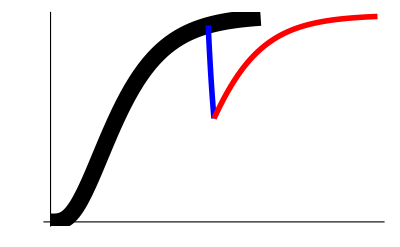

```mathematica
Show[
{
Plot[massfn[100,m0in,ain,x],{x,0,9000000},PlotStyle->{Thickness[.03],Black},Ticks->False,AxesStyle->Thickness[.005]],
Plot[massdecay[100,ain,x],{x,tstart,tfinish},PlotStyle->{Thickness[.01],Blue}],
Plot[massfn[100,50,ain,x-tfinish],{x,tfinish,2*tfinish},PlotStyle->{Thickness[.01],Red},Ticks->False]
},
PlotRange->{All,All}
]
```

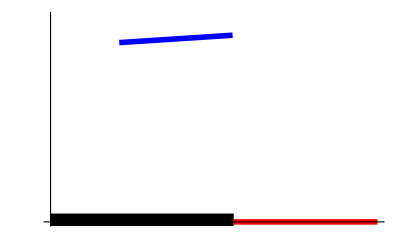

```mathematica
pltout=Show[{Plot[massfn[100,m0in,ain,x],{x,0,8000},PlotStyle->{Thickness[.03],Black},Ticks->False,AxesStyle->Thickness[.005]],Plot[massdecay[100,ain,x],{x,3000,7950},PlotStyle->{Thickness[.01],Blue}],Plot[massfn[100,m0in,ain,x],{x,mintime,8000},PlotStyle->{Thickness[.01],Red},Ticks->False]},PlotRange->{All,{0,110}}]
```

```mathematica
tfinish=x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-95],x>5000000},x][[2]]
```

6.75187×10^6

```mathematica
massfn[100,m0in,ain,tfinish]
```

95.

```mathematica
massdecay[mmax_,a_,t_]:=.95*mmax*E^(-a/mmax^(1/4)*(tfinish-t))
```

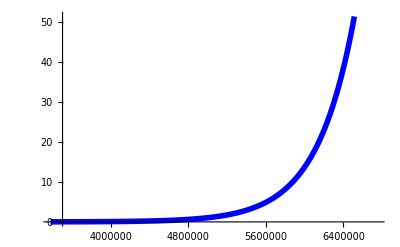

```mathematica
Plot[massdecay[100,ain,x],{x,.5*tfinish,tfinish},PlotStyle->{Thickness[.01],Blue}]
```

```mathematica
massdecay[100,ain,tstart]
```

95.

```mathematica
tstart=x/.NMinimize[{Abs[massdecay[100,ain,x]-50],x>5000000},x][[2]]
tstart2=x/.NMinimize[{Abs[massdecay[100,ain,x]-25],x>5000000},x][[2]]
```

6.50251×10^6

6.23323×10^6

```mathematica
massdecay[100,ain,tstart]
```

50.

```mathematica
mintime=x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-massdecay[100,ain,3000000]],x>5000000},x][[2]]
```

5.50001×10^7

```mathematica
massdecay[100,ain,8000000]
```

3.8232

```mathematica
recoverstart=massdecay[100,ain,.95*tstart]
```

226.528

```mathematica
Plot[massfn[100,50,ain,x],{x,10,2*tfinish},PlotStyle->{Thickness[.01],Red},Ticks->False]
```

-Graphics-

```mathematica
tstart3=x/.NMinimize[{Abs[massfn[100,m0in,ain,x]-50],x>1000000},x][[2]]
```

2.8286×10^6

```mathematica
massfn[100,50,ain,0]
```

50.

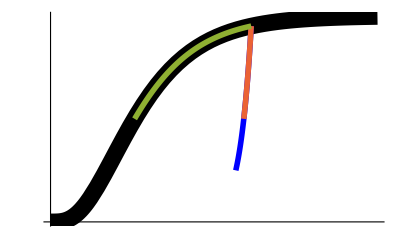

```mathematica
Show[
{
Plot[massfn[100,m0in,ain,x],{x,0,11000000},PlotStyle->{Thickness[.03],Black},Ticks->False,AxesStyle->Thickness[.005]],
Plot[massdecay[100,ain,x],{x,tstart2,tfinish},PlotStyle->{Thickness[.01],Blue}],
Plot[massdecay[100,ain,x],{x,tstart,tfinish},PlotStyle->{Thickness[.01],RGBColor[0.922526,0.385626,0.209179]}],
Plot[massfn[100,50,ain,x-tstart3],{x,tstart3,tfinish},PlotStyle->{Thickness[.01],RGBColor[0.560181,0.691569,0.194885]},Ticks->False]
},
PlotRange->{All,All}
]
```

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

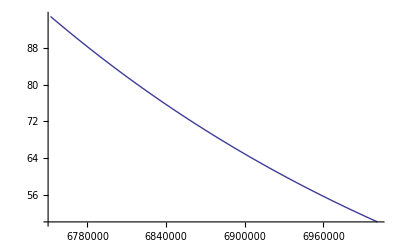

```mathematica
Plot[massdecay[100,ain,x],{x,tstart,tfinish},PlotStyle->PlotStyle->{ColorData[97,4],Transparent,Transparent}]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
ColorData["Indexed"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62}

```mathematica
?ColorData
```

ColorData[scheme] gives a function that generates colors in the named color scheme when applied to parameter values. 
ColorData[scheme,property] gives the specified property of a color scheme.
ColorData[collection] gives a list of color schemes in a named collection.
ColorData[] gives a list of named collections of color schemes.